```mathematica
nMax=1000;
fib[x_,p_,q_,m_]:=RecurrenceTable[{X[n]==Mod[X[n-p]+X[n-q],m],Table[X[i]==x[[i]],{i,1,q}]},X,{n,1,nMax}];
```

```mathematica
nMax=4000;
modulo = 2^10;
seq = Table[RandomInteger[modulo],{i,1,56}];
fib[x_,p_,q_,m_]:=RecurrenceTable[{X[n]==Mod[X[n-p]+X[n-q],m],Table[X[i]==x[[i]],{i,1,q}]},X,{n,1,nMax}];
```

```mathematica
p=24;q=55;m = 23209;
x0 = Table[i,{i,1,q+1}]
56-24
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56}

32

```mathematica
fib[x0,p,q,m]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,33,35,37,39,41,43,45,47,49,51,53,55,57,59,61,63,65,67,69,71,73,75,77,79,58,61,64,67,70,73,76,79,82,85,88,91,94,97,100,103,106,109,112,115,118,121,124,127,107,111,115,119,123,127,131,112,117,122,127,132,137,142,147,152,157,162,167,172,177,182,187,192,174,180,186,192,198,204,210,170,178,186,194,202,210,218,226,234,242,250,258,266,274,282,290,298,283,292,301,310,319,328,337,277,289,301,313,325,337,349,338,351,364,377,390,403,416,429,442,455,445,459,473,487,501,515,529,451,469,487,505,523,541,559,508,529,550,571,592,613,634,655,676,697,695,717,739,761,783,805,827,734,761,788,815,842,869,896,785,818,851,884,917,950,983,993,1027,1061,1072,1107,1142,1177,1212,1247,1282,1179,1220,1261,1302,1343,1384,1425,1236,1287,1338,1389,1440,1491,1542,1501,1556,1611,1643,1699,1755,1811,1867,1923,1979,1874,1937,2000,2063,2126,2189,2252,1970,2048,2126,2204,2282,2360,2438,2286,2374,2462,2527,2616,2705,2794,2860,2950,3040,2946,3044,3142,3240,3338,3436,3534,3149,3268,3387,3506,3625,3744,3863,3522,3661,3800,3916,4056,4196,4336,4361,4506,4651,4589,4743,4897,5051,5205,5359,5513,5023,5205,5387,5569,5751,5933,6115,5492,5709,5926,6120,6338,6556,6774,6647,6880,7113,7116,7359,7602,7845,8065,8309,8553,7969,8249,8529,8809,9089,9369,9649,8641,8977,9313,9626,9963,10300,10637,10169,10541,10913,11032,11415,11798,12181,12426,12815,13204,12558,12992,13426,13860,14294,14728,15162,13664,14182,14700,15195,15714,16233,16752,15661,16250,16839,17152,17753,18354,18955,19073,19695,20317,19674,20351,21028,21705,22359,23037,506,21633,22431,20,795,1594,2393,3192,1093,2018,2943,3569,4507,5445,6383,6033,7027,8021,7497,8557,9617,10677,11576,12643,13710,10982,12214,13446,14655,15888,17121,18354,14757,16200,17643,18764,20221,21678,23135,21694,68,1651,1440,3101,4762,6423,7440,9129,10818,7447,9356,11265,13151,15038,16949,18860,13181,15422,17663,19559,21815,862,3118,22787,2086,4594,5009,7608,10207,12806,13473,16156,18839,14944,17913,20882,619,3405,6383,9361,954,4427,7900,11005,14494,17983,21472,14335,18286,22237,564,4620,8676,12732,11958,16224,20490,16384,21014,2435,7042,10845,15512,20179,8401,13783,19165,947,6323,11723,17123,4307,10499,16691,20123,3226,9538,15850,11536,18310,1875,21393,5413,12642,19848,1109,8459,15809,136,8487,16838,1566,9728,18106,3275,5261,14926,1382,7919,17720,4312,14113,2662,13387,903,21957,10033,21318,9371,13067,1474,13090,16520,6292,19273,8608,20573,10409,245,13662,5500,20547,8866,834,16035,8027,6969,677,17594,18871,13259,7647,2012,1394,19784,14965,14704,11705,8706,5247,21682,18868,16054,13798,13987,14176,10432,10562,10932,11302,12230,15603,18976,3581,7770,11959,16125,4056,9962,15868,13452,21738,6815,14618,11540,20342,5935,7109,20279,10240,19040,7926,21341,11547,2683,21103,16314,12447,8604,4785,943,11025,10639,10253,9114,11788,14462,16630,12934,16917,20900,21813,8775,18946,1078,6399,17000,4392,16481,11881,7281,22879,19166,15717,12245,46,3033,6020,12695,19558,3212,9546,16990,3670,13559,12056,7304,2552,15696,17939,14133,10327,381,8951,17521,18710,3883,13849,583,2729,927,22334,1933,4953,7997,10489,4806,14309,603,21170,19092,17014,9117,7664,7841,8018,22194,17726,13258,19788,10282,7640,4975,19210,12808,6406,1603,910,505,22734,4852,17342,6623,10656,15441,20226,18663,1445,11511,21577,11041,1821,15810,12275,5012,21773,15302,19591,21759,718,20313,4793,14354,108,7581,18269,5748,12589,20394,5014,5943,6251,2611,22180,9002,20913,9615,21392,12676,6405,111,18576,16276,13976,16892,15075,21994,5083,3582,7868,12154,14192,21304,5519,5468,11103,19953,5594,19658,13145,6632,16846,14121,17916,21688,6408,18097,6577,5958,20087,20558,20385,23173,6418,12872,11296,2888,19873,5576,18684,15013,11342,9038,10330,11646,22789,20372,20527,20659,15410,15801,16192,4141,9554,3754,20496,18540,22694,3639,4979,17963,18658,10659,22266,22881,287,21,8425,17165,5048,8266,17271,3044,11859,5737,22824,20987,466,21670,18975,1739,17582,10216,10937,14841,16007,7835,22230,6090,13159,11317,11313,13829,10624,3741,9075,14386,20897,16067,11261,20567,20838,18988,16425,17149,10174,3199,15078,1186,19761,5122,17561,5575,16798,16296,6067,9278,21283,2798,8747,14673,20918,1283,5217,2406,5895,13050,19469,5799,15911,2814,12856,1652,18222,888,19300,23157,3805,4024,20908,2076,5909,1819,14837,4623,9026,12596,19046,13030,9636,22125,10646,3487,8769,14075,10214,22490,14001,17313,13240,10122,7004,19102,22094,21837,11031,19380,20412,21421,2113,18663,5115,11104,12434,7663,2110,1196,10052,19292,12620,5176,3842,13573,19039,2824,9818,8749,537,16850,11919,15471,20360,2017,6137,16362,7191,17013,14253,22500,6733,10222,22648,15129,2441,14812,2758,1010,22526,11593,684,18963,23027,7642,6023,5502,7273,9021,2030,15247,5819,4835,10424,19703,4945,12335,18102,20244,13545,4037,10421,3120,513,21645,19976,8374,4994,11484,19596,1332,10097,18839,10779,15784,22669,16754,2686,16854,6962,18472,11255,4226,7349,18290,9712,9853,10735,21084,11896,10815,19806,14242,20606,649,21690,19523,6533,15602,7102,22777,8188,918,15983,20502,3293,10045,12184,5505,6206,14798,23070,15977,8931,1151,634,1454,517,1162,20126,16290,14907,20596,18586,19164,9520,11015,11613,8072,19077,9505,5729,8191,23060,21760,18333,4023,13157,8500,18924,11166,10370,11897,18001,4977,2513,17193,9619,16561,10169,9496,7927,14605,11470,16607,5297,16379,769,14534,15626,7316,23202,20684,1220,17372,1959,11758,10769,13908,3664,17827,11073,17078,11331,6413,1008,6303,8857,11984,1252,2690,11784,2938,489,3184,9498,3204,9411,17223,510,6882,14792,3856,12164,13542,22239,4239,19,1205,5985,8816,2841,21603,17813,12859,21280,10865,15094,14654,2896,8501,2581,17992,15044,22508,22108,3849,9639,14762,16402,6198,11777,11974,19893,12480,20668,9467,11682,981,4484,11873,21397,302,14880,9753,5271,6567,17982,22997,2083,13347,12843,964,10416,6708,18659,3557,540,1435,11001,8497,15921,1000,5689,17858,7004,3143,13274,4357,18130,4638,5638,14882,16737,16243,21344,3545,5199,21752,17958,2456,4389,11074,2554,1690,22119,12777,17663,14542,19484,602,22741,16039,19111,9122,17511,13070,17039,7914,7888,8816,11766,16525,17746,4539,17736,708,3518,12106,5618,8227,21220,15082,20919,11603,8029,8751,20111,14811,12160,20074,20182,21188,12245,3737,16404,22163,9419,21276,10770,22052,7063,17305,4161,2976,467,19471,8784,14157,9719,7661,9679,9265,3493,16349,20784,20720,5075,22848,2317,16465,22489,15106,18684,6731,15879,5862,20686,20722,5006,13998,9492,17675,21825,13279,17906,7276,18575,14059,9178,5540,13826,19750,17128,5416,19354,12079,16663,18976,19616,22266,19640,6932,3073,1559,8335,1529,15921,17440,20882,7743,14837,22843,126,15259,21487,6220,3184,8909,12494,9654,14174,842,19255,1374,12896,6212,18179,20243,15066,17408,21783,14917,18395,12749,5626,9126,17801,13875,11557,917,10460,4275,3344,18832,19714,14668,15796,18502,18312,2357,7049,13697,10833,13815,20840,11348,2118,15822,7185,17461,19330,6587,5788,21799,18203,19112,2978,18958,11764,12946,22016,21686,4012,14851,16703,4662,11675,9861,22214,1035,8330,10792,4219,9318,13529,5161,20705,16985,7743,1529,12104,13550,2430,1294,22933,8937,8287,18195,12326,1167,3134,2448,17507,19347,10687,17841,17916,20151,4135,2792,8844,19103,356,8714,6356,9671,9017,7082,21523,3931,4190,21173,8075,12931,16080,1255,15984,150,2329,11335,22578,8617,13996,1797,9879,4224,11148,12933,15674,23200,14178,4578,15299,11674,5719,10068,21625,15361,17374,979,1712,8437,20524,452,536,11751,16444,19304,6017,14911,5780,7640,12616,4126,16970,13422,11193,12030,14433,16424,8087,1169,1247,22502,5643,12627,18488,8527,13467,4622,17699,12079,6167,17240,17115,7009,21233,18122,18767,92,15417,23178,4157,8889,8078,15347,5825,14592,17317,18346,5347,6943,5619,21996,18678,13791,14604,14555,17567,7545,9775,11357,14862,6109,7119,5749,11797,21505,12204,9108,19247,2576,6138,9570,21771,15030,6788,34,17971,19434,4022,9834,2885,21012,14397,5847,3732,12276,1150,22864,18806,19529,7117,4666,19339,17993,6107,13727,7451,23108,22135,5859,9354,13542,22368,15181,9828,3422,13184,1316,17523,3671,15705,17222,3142,6095,18474,19528,2239,1903,11856,2315,5747,12103,8034,1897,11930,19680,8729,13743,1649,10210,13218,19287,13748,7693,2330,20107,945,20492,1112,51,14515,3053,11511,21121,2067,19220,12700,21236,6714,2578,22456,21194,1548,9136,19077,5432,4081,6852,17511,6726,4367,10467,2428,17574,18186,18758,5524,1054,8162,14485,9019,266,8617,14434,1562,3732,13651,17170,20974,17362,552,15581,8045,8375,14577,476,21715,8113,2670,21088,2422,1999,5445,15597,9070,14781,11670,2736,22683,5799,9662,6661,19001,867,3130,14828,6030,9923,504,19553,3938,12194,9522,15390,9148,6366,15912,18025,3435,9758,7219,8260,528,13961,938,15680,19267,9484,17564,16390,9762,365,17674,17318,21300,12746,1894,226,17523,20943,16388,16531,11548,12428,5098,10682,2527,19406,16535,1541,10839,21154,20300,15864,15561,10027,1126,13110,22167,15876,16722,6256,4237,21447,12732,20469,533,21950,20488,19830,8893,12109,11351,4976,20597,5164,5351,16392,6313,10965,16806,9168,8442,10231,9903,16018,4602,15912,6841,18560,13279,635,20714,14144,6627,5288,4673,16524,9816,10262,16033,18919,2510,4291,18347,20007,6387,7322,2558,8370,14629,17038,19951,17518,5946,17357,3761,18381,4865,18020,1933,17057,8557,7541,12654,4603,14619,15642,114,17395,11551,12673,18950,14683,2385,10635,5910,2751,16177,4051,19779,22983,20777,1652,20493,7127,9192,5046,3589,11230,19907,20315,16638,4002,21813,5497,14660,17193,6676,5773,2708,9138,290,6609,4940,14403,14606,21603,14802,13073,3340,8807,21970,16095,14718,22248,10486,12559,6145,18151,19263,8603,22318,5887,20103,20689,12963,2350,19623,16788,2032,4304,17553,6041,7391,5377,21744,13663,16370,19532,17613,21751,11191,21740,7284,5301,19424,22525,896,19293,18460,17010,13607,255,7805,7012,3482,6331,14000,10317,12938,5060,14764,11125,7477,1882,19998,20501,170,20019,18463,9802,13455,2229,13402,13064,22210,22573,13692,3906,962,19294,16350,6731,6517,7092,19068,5469,13518,9273,2166,19036,13833,13180,14786,4206,11997,13420,11933,20348,4302,18788,13008,4802,20255,14545,10151,20338,6772,14897,2871,8951,19849,64,12483,8765,18893,4735,2702,11683,13879,10209,9225,20518,1112,14042,22810,18257,22484,4738,6,19339,6136,5380,6777,9913,15934,16414,19214,15282,2776,594,8171,1992,23152,12375,5052,11142,14292,5619,3807,7045,12695,16671,20354,432,1715,18388,11579,6959,7270,3356,16343,22054,17673,3465,17122,21841,7,1649,13817,6826,19027,8321,15490,20924,22904,2687,17663,1544,15757,17989,6627,6234,12008,3362,12473,4981,23053,10242,3826,14566,16421,20863,5890,9602,19621,16492,17482,20867,12070,7739,5596,15836,21376,21796,13672,18929,5470,507,12905,6696,18232,21821,10785,21836,19777,13997,4735,4066,23086,10405,16114,20874,13719,21556,12422,11654,6488,14077,11387,18624,8157,18170,14449,22453,13012,5239,17019,10635,23139,3261,9716,3910,10119,14231,7471,14086,11373,4237,22024,8066,22980,8350,9045,7485,15896,557,7076,20620,11599,18911,12739,16105,437,16166,16412,22142,8731,1807,6098,10654,2161,8972,2881,7943,10176,1255,6710,21204,14243,12979,18730,3899,2467,7089,8154,1053,18607,7406,15656,11945,13970,18826,16733,10584,5422,18688,6791,18062,1198,8726,20796,9368,18480,11794,3587,3670,10817,16134,15639,16949,19164,14482,13067,335,9672,8356,9629,11021,21588,11891,5724,3584,3005,14824,8241,11529,4243,14675,11530,13846,12072,22844,13634,7983,8934,10003,16966,2802,16761,16510,10682,6419,5785,4338,17669,17554,21831,8348,18825,16951,22931,21466,6383,15044,20798,20431,23002,3254,20728,13590,20636,13619,9686,8940,4422,2374,20267,17405,18004,4017,6978,17977,6637,15330,11613,3981,9967,18049,12413,5463,11322,7497,12194,1911,11273,2482,9321,22574,12405,11308,7061,11162,20806,20778,279,5450,13056,21115,15951,21650,4312,16671,20761,1079,5064,7219,10451,8294,3108,71,6543,22367,15659,8827,20651,8589,11216,7255,9219,9872,15430,18173,10147,16445,8329,440,15529,7716,20394,18832,14432,18261,21157,12484,12006,10480,23156,21021,22562,19862,13698,16576,8584,22277,3529,2025,21309,14042,5898,719,20979,20772,18300,11574,12873,22573,14619,10036,13085,15544,7166,8263,7647,22970,13769,23119,7742,14727,12356,22676,6689,2049,13153,9938,7642,12993,13264,21721,6109,7693,15059,2356,20801,12729,2789,22695,2699,20918,3044,11916,18222,14674,10168,22029,3342,15747,6520,18522,6710,16522,15289,19821,20151,13591,15778,126,18364,7820,14363,12359,2063,12328,13080,1792,10557,21840,18431,6467,3103,6307,6430,3055,21437,5669,14756,3301,22200,3535,2507,7768,8148,21084,12875,18468,9756,4178,15436,22593,77,1420,17917,9166,812,9351,18346,21277,12902,15837,13576,6643,14738,10055,21029,14478,1461,13164,9487,15410,138,19956,15562,17748,7897,15783,7067,11229,13140,22431,20138,8625,11533,11059,20043,9746,21045,16485,875,12706,7130,4711,12788,14401,3673,22463,121,2687,5772,5449,2326,20985,17318,14658,19522,8702,12953,5767,6000,10558,7187,11622,22152,2399,22967,18287,19431,5930,13728,20283,14599,4148,18936,14936,17736,21123,14065,7011,14061,16599,5527,12834,17229,489,6409,8551,7568,13932,10817,15121,5968,3766,7004,21158,4096,11278,438,4515,8928,1587,13319,7132,16748,22371,10976,15160,15005,17807,21067,4864,16270,3676,16584,21121,16526,10953,18626,20101,6495,11036,18725,737,14858,15315,10393,21731,20896,18098,2703,9687,12919,8663,4869,18925,9660,9203,6209,15141,17015,17362,3968,4460,20427,21853,10637,6705,18624,22319,8342,2618,8965,18536,7218,18615,14506,21982,12001,12464,8822,20179,21369,6937,11613,15220,8832,20730,894,15228,8549,22,6368,17736,5234,9113,20001,14052,7955,10264,6612,9166,10523,10151,3711,22882,7847,19856,20276,20089,4548,7181,10097,21437,481,17037,521,21704,9694,6331,18645,1480,14660,5679,5722,17508,13141,19116,22247,6891,3253,11153,19049,8881,17012,16003,7067,19597,7418,5441,15741,7327,7215,7225,10664,10029,14682,12047,249,22742,22254,15908,13090,14846,13517,17765,5006,19404,3954,19714,6740,4235,4065,2508,12621,11875,14396,17322,8892,10510,8510,12568,21953,9227,5376,11344,14570,6297,19196,278,22514,9336,23070,18752,13631,7488,15218,21557,21502,5678,7190,1180,5280,17928,13951,5100,6071,16442,12601,22008,1390,20979,8034,527,22047,8381,15769,8633,5268,21005,9774,3354,17697,9632,3695,7920,9515,21993,16459,17721,17946,7629,6714,7691,11900,6280,20602,22480,8065,13757,3904,23203,11565,16992,10052,2659,3824,9493,22447,21551,17003,14002,14807,16014,415,14819,7894,12971,6619,20231,2493,5342,1298,3149,2703,1384,9335,1817,10579,1497,12205,2053,7871,3610,14799,567,18161,10502,10047,18514,15814,22486,5403,13481,20214,79,8927,9863,10394,13284,15615,22419,9850,9562,2753,5957,7865,15175,8582,10619,20820,14326,19540,17752,14156,16280,19405,5079,13019,494,537,17757,156,19903,12637,1703,15192,10860,5902,8660,9249,1301,10399,21198,22317,3322,21593,2414,17766,7870,19972,31,312,10541,19051,10362,22642,2097,2909,21917,15271,19787,15765,19054,22533,16916,9609,7839,8670,6075,4341,10279,9732,16452,7382,20851,14638,6872,13594,1309,15713,21502,7988,11727,15765,20324,10313,19210,19227,6344,11312,23031,19530,11977,13001,19528,11033,3642,5371,19959,17960,5256,16008,19075,374,18265,8019,12039,3097,16166,20675,18643,21324,9253,10020,15093,16108,4533,8846,18852,4740,13251,13210,5420,826,9597,3078,5598,16826,2438,5661,3468,9969,6551,21984,11147,19617,17241,21747,7649,13223,14846,4847,14870,11084,1354,13032,1741,12803,22598,22606,16631,20468,7809,2411,21428,15225,22559,17850,11521,14673,2051,10577,10746,6180,12312,281,12985,20337,11374,4916,17849,17336,8235,18249,21371,10510,21019,7831,22254,1613,2428,239,5138,17111,7712,14045,20715,12731,11087,11428,9393,14369,9912,12565,7863,8973,13082,9910,9246,11864,10842,9572,11848,1002,1825,16870,2397,1711,10123,12264,12731,12081,5728,22949,857,16420,20489,102,14043,21285,13363,22895,6374,29,15758,4212,5975,9237,20074,15032,12907,22730,17954,11309,14344,14509,5967,4878,17968,923,11325,20817,3565,9163,1582,9079,20743,9941,5114,12075,14948,22319,6775,1069,1562,10363,4317,23157,15346,16334,22837,7275,19679,11046,380,10339,15646,14891,1322,9936,13954,7221,5216,2909,13024,12473,6461,7443,1591,2912,8529,5923,1374,13199,14660,20182,19200,5791,11689,1474,6946,20858,6200,4695,14877,18546,2824,6474,22187,14055,15540,4977,11532,8026,20604,20871,484,19974,15729,21744,6354,10108,11637,16820,71,20486,13475,1165,2714,18926,13163,22120,13869,15377,2267,18931,18753,13242,304,10686,12957,3226,23172,126,9266,18637,17560,18194,13270,11937,10448,20365,8505,7406,14637,5857,11518,21577,6962,10599,14090,16066,6778,9664,3803,18766,4940,11658,17292,16032,15222,18678,10035,4457,8983,3510,18613,19043,8248,5928,8795,11843,8127,13313,9807,6020,5689,324,19180,21033,662,7202,7325,16336,2699,8426,13261,4420,9109,12776,14041,13394,3233,19198,20732,22291,5283,21818,17213,20657,11546,11842,17548,4786,11261,21292,182,23114,12363,12229,8818,9360,20767,6859,6864,5407,21911,6024,1980,8065,8793,17222,13047,5696,17474,20637,6182,12913,1365,7890,6202,5594,12687,8200,6642,10022,4760,14184,23200,8106,7128,19285,6400,17174,21569,8054,3232,8929,13463,18160,5264,18196,23183,1894,3650,17140,1320,2539,11428,21283,2843,14366,23105,20469,19357,4894,15760,14732,5219,14918,8639,7631,19487,20140,13329,3780,17196,14941,9346,11405,21957,8721,1132,22648,10733,20568,5490,9947,4348,11536,2573,19492,19403,14909,16745,14759,15563,3331,7294,2140,2041,18173,18275,1659,16908,13985,19328,22622,12627,1009,22630,11267,6887,22964,647,22335,10560,14805,14005,10907,20457,19091,22026,7359,16959,3603,2697,21146,13839,4105,23108,16609,4359,10355,10826,10015,15608,887,86,9859,7919,20295,743,15255,8784,21664,18309,3553,8659,20348,17456,13500,17170,11399,2039,18650,22532,5421,12485,3714,6384,20215,22708,22486,8928,19716,12010,22142,8539,22311,17435,14113,255,11144,5154,10748,13052,10216,9398,12400,2926,8118,10422,17553,10489,20114,16108,3636,19283,7333,22025,14541,9426,22397,4085,22032,20550,11887,20409,19532,11507,5316,12951,21059,65,2365,713,11514,21888,22153,11549,2959,1495,19818,2530,20925,6432,21896,3362,7751,17057,688,19342,4862,10609,22751,3855,21314,11209,7519,11461,1357,8895,8342,740,5885,9613,7031,20083,8205,3337,14795,6998,3825,1181,22713,10674,14288,9797,3627,2678,18655,23096,4719,7784,12864,14211,21293,21799,5950,11978,7744,8388,6884,2281,3135,9957,5320,20999,2034,8390,20720,8484,6989,10429,12503,575,852,12646,264,13753,1939,19904,17159,19497,19205,9745,15779,10623,3875,15842,14933,4821,22117,16595,848,70,13987,14254,13684,79,11526,3725,10061,17380,4617,15350,17046,1007,3780,22609,6781,8707,2465,21792,3702,12565,7296,270,3129,3205,735,19574,11474,2113,19916,1236,18545,1160,15046,4644,17621,1859,16426,22873,20534,10646,22369,15742,23199,8561,17041,16049,13752,7080,16577,11298,16295,1021,13302,2084,18615,15147,6091,18328,17700,13385,20151,9725,14705,15263,14510,9579,997,12341,16441,22830,22459,9545,15160,15000,5651,8317,13572,5213,21820,15882,2456,6593,19813,10092,21387,5061,15865,7100,19154,3991,2856,5558,16105,20155,9896,8705,7693,14990,14212,2149,6412,18965,5691,9250,13754,22888,20834,185,262,467,7803,13191,14273,21691,16241,2500,2621,11651,1950,6,17272,15987,3344,18590,6033,18215,15236,1201,5545,5330,5942,13757,5475,22287,476,15647,20866,18295,3124,678,7682,4307,9050,19160,21263,18843,8902,11486,2979,4902,732,8894,20535,19542,8091,20169,1231,4769,9726,6192,20545,15920,3309,940,8149,12110,22241,10224,19745,11875,11402,14107,14630,6852,738,2957,13313,22886,3472,2993,19446,20005,10927,11737,2666,21862,17066,6415,7227,12586,14679,7881,14831,14999,12080,21789,18937,15902,19898,1011,8947,8579,14958,5972,1139,20737,19821,9063,22208,6744,14026,7646,11996,22312,20871,5217,7542,18308,13020,6729,7838,14934,6913,20756,20822,19981,5856,20602,7991,21475,22778,22376,21885,10216,17019,3883,8792,10030,9399,7883,6195,12165,19435,13956,20424,6404,14794,12378,12612,8852,4436,16330,684,18164,580,8114,7255,1965,22991,5022,6320,6642,18462,6882,12939,2982,3872,2743,19527,4066,20011,19920,7711,21872,11165,959,15618,1868,21336,5727,4027,7821,20384,13013,4586,6211,17629,5558,23155,20001,7755,11535,6348,13465,4685,2906,19876,18098,1912,21383,22022,16662,10505,18339,12879,12257,13505,13697,22750,6791,2534,12813,1911,19783,12777,17855,12990,8718,11567,15845,22858,21970,4655,17701,2879,13464,7216,2841,11542,213,14464,6106,1409,4918,8261,16840,9732,16958,2581,22441,19201,3138,17125,15791,19650,6516,16190,840,16344,18149,10122,22717,6431,2125,12638,4919,18071,15423,3391,6510,21989,7254,16278,21982,2783,5672,6729,17702,16224,19293,10836,13830,1853,6507,2758,22366,5192,6780,7130,7798,8326,22639,6232,18052,22202,21718,22384,182,7701,13933,360,4225,9973,21874,10068,9822,4991,423,18549,18807,11708,22970,7970,933,3266,9552,5740,1274,1118,11147,4094,18253,23124,17324,6870,3005,17227,14943,8841,12605,10663,7152,13042,11822,7792,10597,21800,2786,9773,12310,4897,6466,7898,18277,11892,3370,22554,347,1713,1998,15736,14118,9023,20306,1387,7512,17267,21795,6457,20665,8413,7777,10196,7650,495,18174,7659,3038,12825,6636,8897,6087,2987,3116,3674,18212,4067,20221,18711,14382,20272,15813,21400,6297,21018,18440,17348,20692,12317,2757,18256,1629,15611,16409,21207,10984,9453,11014,21951,6895,7437,19566,19058,16095,22270,8340,12309,15320,18115,19827,1651,14750,10903,9214,15712,10042,179,3396,5648,11479,4418,18673,1780,19720,14073,5254,1936,19082,2177,12014,7312,19387,15127,15329,16033,11813,3507,7405,22009,7851,18619,20744,3131,587,7175,13720,3409,12122,7273,3252,12920,5326,13191,10756,14207,3615,11484,11178,8919,10874,11847,19714,14120,2757,15237,22395,17881,11490,16389,6223,13451,12301,10669,8900,1190,9744,8655,12536,10718,17688,16738,13114,4792,13051,652,3817,10298,17884,7357,15219,6485,14997,585,5023,21302,7711,8204,12031,1777,16919,22375,15945,22840,1752,19990,2825,10118,3033,11408,18024,13913,6159,18535,929,17359,3635,20299,19143,850,22948,7390,6703,13267,10099,5389,6187,11932,12421,5681,4015,19862,11688,735,5533,8392,22897,8440,5721,7201,4287,907,6232,18734,7096,22609,13188}

```mathematica
|
```

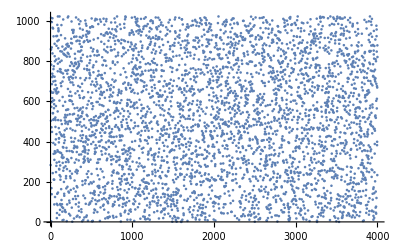
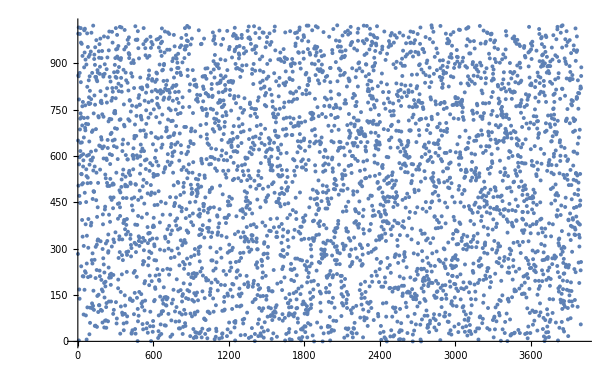
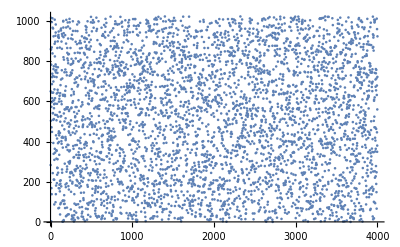
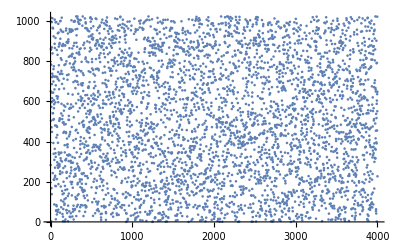
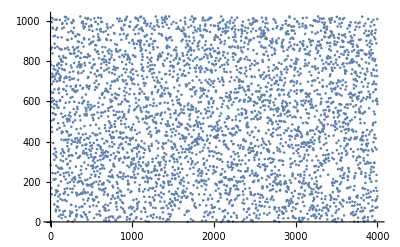
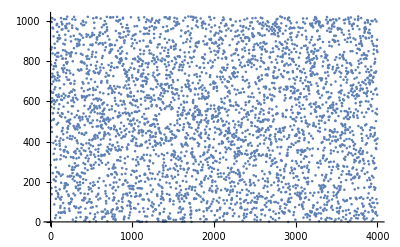
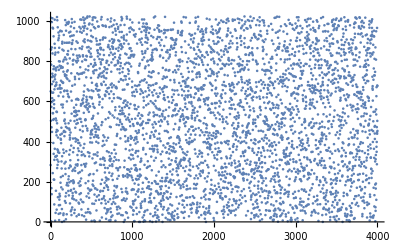
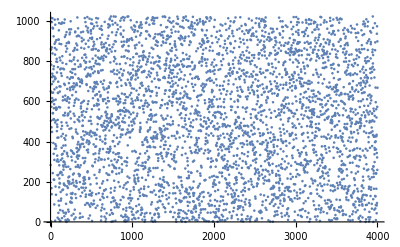
{{{-Graphics-,p=23,q=50},{-Graphics-,p=23,q=51},{-Graphics-,p=23,q=52},{-Graphics-,p=23,q=53},{-Graphics-,p=23,q=54},{-Graphics-,p=23,q=55},{-Graphics-,p=23,q=56},{-Graphics-,p=23,q=57}},{{-Graphics-,p=24,q=50},{-Graphics-,p=24,q=51},{-Graphics-,p=24,q=52},{-Graphics-,p=24,q=53},{-Graphics-,p=24,q=54},{-Graphics-,p=24,q=55},{-Graphics-,p=24,q=56},{-Graphics-,p=24,q=57}},{{-Graphics-,p=25,q=50},{-Graphics-,p=25,q=51},{-Graphics-,p=25,q=52},{-Graphics-,p=25,q=53},{-Graphics-,p=25,q=54},{-Graphics-,p=25,q=55},{-Graphics-,p=25,q=56},{-Graphics-,p=25,q=57}},{{-Graphics-,p=26,q=50},{-Graphics-,p=26,q=51},{-Graphics-,p=26,q=52},{-Graphics-,p=26,q=53},{-Graphics-,p=26,q=54},{-Graphics-,p=26,q=55},{-Graphics-,p=26,q=56},{-Graphics-,p=26,q=57}},{{-Graphics-,p=27,q=50},{-Graphics-,p=27,q=51},{-Graphics-,p=27,q=52},{-Graphics-,p=27,q=53},{-Graphics-,p=27,q=54},{-Graphics-,p=27,q=55},{-Graphics-,p=27,q=56},{-Graphics-,p=27,q=57}},{{-Graphics-,p=28,q=50},{-Graphics-,p=28,q=51},{-Graphics-,p=28,q=52},{-Graphics-,p=28,q=53},{-Graphics-,p=28,q=54},{-Graphics-,p=28,q=55},{-Graphics-,p=28,q=56},{-Graphics-,p=28,q=57}},{{-Graphics-,p=29,q=50},{-Graphics-,p=29,q=51},{-Graphics-,p=29,q=52},{-Graphics-,p=29,q=53},{-Graphics-,p=29,q=54},{-Graphics-,p=29,q=55},{-Graphics-,p=29,q=56},{-Graphics-,p=29,q=57}}}

```mathematica
Table[{ListPlot[fib[seq,p,q,modulo]],"p="~~ToString[p],"q="~~ToString[q]},{p,23,29},{q,50,57}]
```